# Narciso Cluster Analysis

### Using Mathematica to investigate variations in samples from Porto

## Header

### Standard Header Section

```mathematica
Needs["HierarchicalClustering`"]
Needs["ProteomicsAnalysis`"]
Needs["ManualPCA`"]
Needs["PrincipalComponentsVariance`"]
Needs["VennDiagram`"]
Needs["Sanitized`"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\cygwin64\home\Andrew\Dropbox\shared_AL\Porto_iTRAQ_neutral-sites

```mathematica
FileNames[]
```

{13211_iTRAQ2-pepts.xls,13211_iTRAQ2-quants.xls,13212_iTRAQ1-pepts.xls,13212_iTRAQ1-PHENYX.xls,13212_iTRAQ1-quants.xls,.git,neutral_sites_investigation.nb,porto_iTRAQ1-EASYPROT.xlsx,porto_iTRAQ1_peptide-data.csv,Porto_PCA_iTRAQ1.pdf,Porto_PCA_iTRAQ2.pdf,ProteomicsAnalysis.m,README.md}

## Protein investigation

### Import data

```mathematica
proteins1=Import["13212_iTRAQ1-quants.xls"][[2]];
proteins2=Import["13211_iTRAQ2-quants.xls"][[2]];
proteins1//Dimensions
proteins2//Dimensions
```

{464,66}

{631,66}

### Collect intersecting proteins

```mathematica
acValues1=proteins1[[3;;All,1]];
acValues2=proteins2[[3;;All,1]];
```

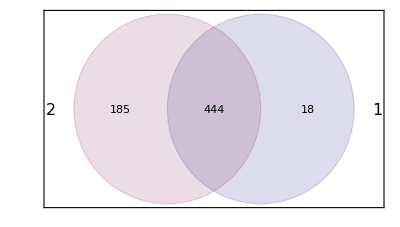

```mathematica
VennDiagram[{acValues1,acValues2}]
```

```mathematica
sharedProteins=Intersection[acValues1,acValues2];
Dimensions[sharedProteins]
```

{444}

### PCA of intersecting proteins

```mathematica
proteinIntensities1=Map[Association@@Thread[acValues1->#]&,proteins1[[3;;All,27;;34]]ᵀ]; (*Isotopic correction, Median correction, Log Values*)
proteinIntensities2=Map[Association@@Thread[acValues2->#]&,proteins2[[3;;All,27;;34]]ᵀ];
```

```mathematica
sharedProteinIntensities=Table[f[[All,Key[sharedProteins[[k]]]]],{k,Length[sharedProteins]},{f,{proteinIntensities1,proteinIntensities2}}];
sharedProteinIntensities=Flatten[Transpose[sharedProteinIntensities,{3,1,2}],1]ᵀ;
```

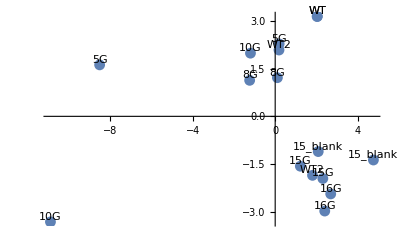

```mathematica
labels={"WT","WT2","15G","15G","16G","16G","15_blank","15_blank","WT","WT2","5G","5G","8G","8G","10G","10G"};
pca=PrincipalComponents[sharedProteinIntensitiesᵀ];
ListPlot[pca[[All,1;;2]],Epilog->Table[Text[labels[[i]],pca[[i,{1,2}]],{0,-2}],{i,16}],PlotRangePadding->Scaled[.1],PlotRange->Full]
```

Not meshing properly based on WT2 positioning.

## Peptide investigation

### Import data

```mathematica
rawPeptideData1=Import["13212_iTRAQ1-pepts.xls"][[1]];
rawPeptideData2=Import["13211_iTRAQ2-pepts.xls"][[1]];
Dimensions[rawPeptideData1]
Dimensions[rawPeptideData2]
```

{8000,20}

{14815,20}

### Putting the data into a workable format

```mathematica
heads=rawPeptideData1[[1,All]];
workingPeptideData1=rawPeptideData1[[2;;All,All]];
workingPeptideData2=rawPeptideData2[[2;;All,All]];
```

```mathematica
heads[[11;;18]]
labelIntensities1=workingPeptideData1[[All,11;;18]];
labelIntensities2=workingPeptideData2[[All,11;;18]];
```

{113.1,114.1,115.1,116.1,117.1,118.1,119.1,121.1}

### Removing empty rows and null intensity data

```mathematica
noSpaceIntensities1=Pick[labelIntensities1,#,False]&[Thread[workingPeptideData1[[All,1]]==""]];
noSpaceIntensities2=Pick[labelIntensities2,#,False]&[Thread[workingPeptideData2[[All,1]]==""]];
```

```mathematica
sanitisedPeptides1=noSpaceIntensities1/.""->0.;
sanitisedPeptides2=noSpaceIntensities2/.""->0.;
```

### Mapping associations ???

```mathematica
acValuesPeptides1=workingPeptideData1[[All,2]];
acValuesPeptides2=workingPeptideData2[[All,2]];
```

```mathematica
a1=Table[Map[AssociationThread[workingPeptideData1[[All,i]]->#]&,sanitisedPeptides1ᵀ],{i,{2,3}}];
a2=Table[Map[AssociationThread[workingPeptideData2[[All,i]]->#]&,sanitisedPeptides2ᵀ],{i,{2,3}}];
```

```mathematica
b1=Map[AssociationThread[heads[[11;;18]]->#]&,sanitisedPeptides1];
b2=Map[AssociationThread[heads[[11;;18]]->#]&,sanitisedPeptides2];
c1=b1;
c2=b2;(*For comparison*)
```

```mathematica
Values@a1[[1]]//Dimensions
Values@b2//Dimensions
```

{8,540}

{14814,8}

### Normalising the data

#### By Channel Sum

```mathematica
Table[Total[sanitisedPeptides1[[All,i]]],{i,8}]
Table[Total[sanitisedPeptides2[[All,i]]],{i,8}]
```

{6876.62,6125.97,5659.23,6833.95,6678.35,5251.11,5762.09,5380.86}

{14755.3,12179.7,12547.4,12265.7,15007.9,11243.6,10938.3,9453.6}

```mathematica
channelNormalisedPeptides1=Table[
(Total[sanitisedPeptides1[[All,8]]]/Total[sanitisedPeptides1[[All,i]]])*sanitisedPeptides1[[All,i]],{i,8}]ᵀ;
channelNormalisedPeptides2=Table[
(Total[sanitisedPeptides1[[All,8]]]/Total[sanitisedPeptides2[[All,i]]])*sanitisedPeptides2[[All,i]],{i,8}]ᵀ;
```

```mathematica
Table[Total[channelNormalisedPeptides1[[All,i]]],{i,8}]
Table[Total[channelNormalisedPeptides2[[All,i]]],{i,8}]
```

{5380.86,5380.86,5380.86,5380.86,5380.86,5380.86,5380.86,5380.86}

{5380.86,5380.86,5380.86,5380.86,5380.86,5380.86,5380.86,5380.86}

#### By median correction

```mathematica
b2=c2;
normalised=Association@@Table[
log=Log[#⟦All,Key[k]⟧];
p=Flatten[Position[log,Indeterminate]];
min=Sanitized[Min][N[log]];
log=N[log]/.Indeterminate->min;
{L,M,R}=Quantile[log,{0.4,0.5,0.6}];
n=(log-M)/(R-L);
n⟦p⟧=-∞;
k->n,

{k,heads[[11;;18]]}];&[b2]
Do[b2⟦All,Key[k]⟧=Exp[normalised⟦Key[k]⟧],{k,heads[[11;;18]]}]
```

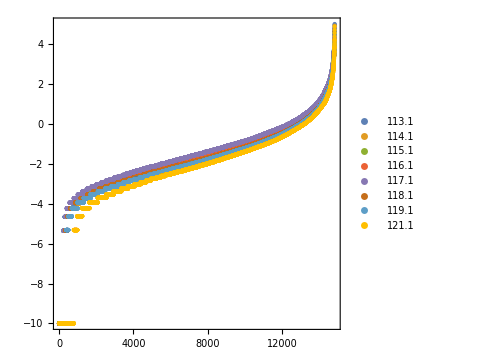

```mathematica
ListPlot[Evaluate@Table[Sort[N[Log[c2⟦All,Key[k]⟧/.(0|0.->Exp[-10.])]]],{k,heads[[11;;18]]}],PlotRange->All,Frame->True,AspectRatio->1,ImageSize->Medium,PlotLegends->heads[[11;;18]],PlotStyle->PointSize[Medium]]
```

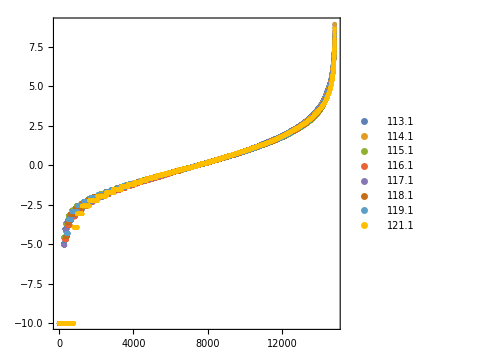

```mathematica
ListPlot[Evaluate@Table[Sort[N[Log[b2⟦All,Key[k]⟧/.(0|0.->Exp[-10.])]]],{k,heads[[11;;18]]}],PlotRange->All,Frame->True,AspectRatio->1,ImageSize->Medium,PlotLegends->heads[[11;;18]],PlotStyle->PointSize[Medium]]
```

### Cluster Analysis

Clusters before normalisation

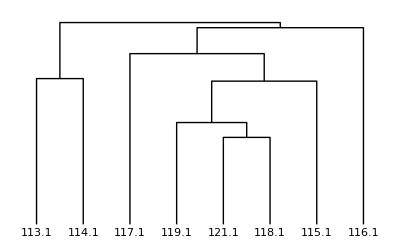

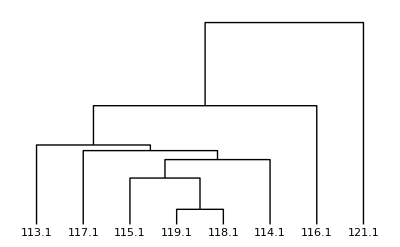

Clusters after normalisation

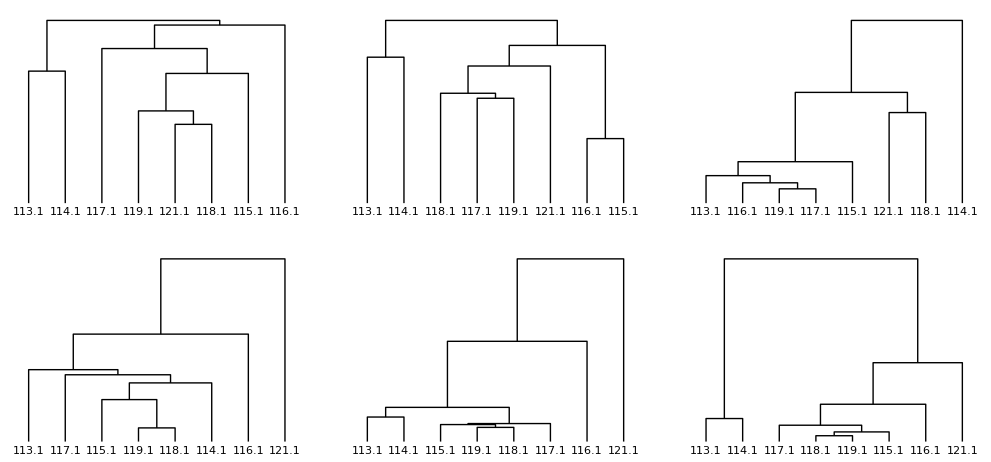

```mathematica
GraphicsGrid[{{"iTRAQ1",
DendrogramPlot[sanitisedPeptides1ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[normalisedPeptides1ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@bᵀ,LeafLabels->heads[[11;;18]]]},
{"iTRAQ2",
DendrogramPlot[sanitisedPeptides2ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[normalisedPeptides2ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@b2ᵀ,LeafLabels->heads[[11;;18]]]}}]
```

### PCA

```mathematica
pca1a=PrincipalComponents[normalisedPeptides1ᵀ];
pca1b=PrincipalComponents[Values@b1ᵀ];
pca2a=PrincipalComponents[normalisedPeptides2ᵀ];
pca2b=PrincipalComponents[Values@b2ᵀ];
```

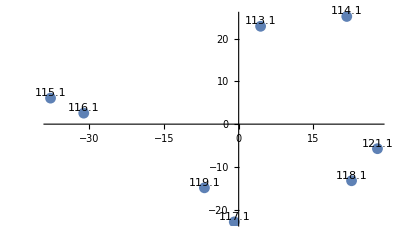

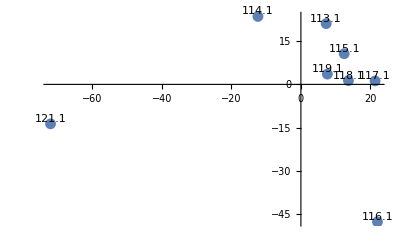

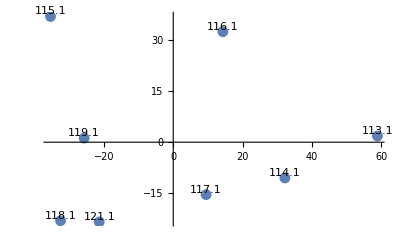

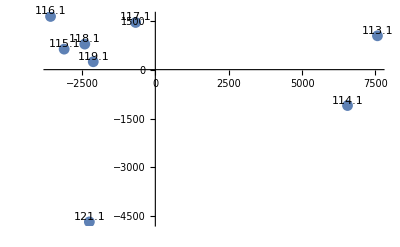

```mathematica
pcaPlot1a=ListPlot[pca1a[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca1a[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]]
pcaPlot2a=ListPlot[pca2a[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca2a[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]]
pcaPlot1b=ListPlot[pca1b[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca1b[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]]
pcaPlot2b=ListPlot[pca2b[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca2b[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]]
```

```mathematica
Export["Porto_PCA_iTRAQ1.pdf",pcaPlot1]
Export["Porto_PCA_iTRAQ2.pdf",pcaPlot2]
```